Part::partw: Part {1,2} of x[t] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part {1,2,3} of InterpolatingFunction[{{0.,6.25146}},{5,3,2,{50},{4},{1},0,0,0,Automatic,{},{},False},{{0.,5.9638×10^-6,0.0000119276,«45»,6.14909,6.25146}},{{{499.,0.,0.,1.},{-21.2132,48.6824,0.,0.},{3.16004,3.16004,0.,0.}},{{499.,0.000290332,0.,1.},{-21.2132,48.6824,0.,0.},{3.16002,3.16002,0.,0.}},{{499.,0.000580665,0.,1.},{-21.2132,48.6825,0.,0.},{3.16,3.16001,0.,0.}},«45»,{{380.237,321.838,0.,1.},{-22.0561,53.6033,0.,0.},{-2.6326,-0.039213,0.,0.}},{{377.965,327.326,0.,1.},{-22.3314,53.5974,0.,0.},{-2.74737,-0.0765508,0.,0.}}},{Automatic}][t] does not exist.

Part::partw: Part {1,2,3} of InterpolatingFunction[{{0.,3.79937}},{5,3,2,{39},{4},{1},0,0,0,Automatic,{},{},False},{{0.,3.97477×10^-6,«35»,3.65777,3.79937}},{{{499.,0.,0.,1.},{-21.2132,69.8956,21.2132,0.},{3.16004,-2.11693×10^-15,-3.16004,0.}},{{499.,0.000277819,0.0000843176,1.},{-21.2132,69.8956,21.2132,0.},{3.16002,-1.75935×10^-6,-3.16003,0.}},«35»,{{427.941,253.635,63.9029,1.},{-20.2259,68.2926,14.5153,0.},{-1.72345,-0.940543,-1.63494,0.}},{{425.059,263.296,65.9417,1.},{-20.4827,68.1552,14.2821,0.},{-1.90447,-1.00076,-1.65878,0.}}},{Automatic}]«1»«1»] does not exist.

Part::partw: Part {1,2,3} of InterpolatingFunction[{{0.,2.46857}},{5,3,2,{32},{4},{1},0,0,0,Automatic,{},{},False},{{0.,3.18667×10^-6,6.37333×10^-6,«27»,2.45285,2.46857}},{{{499.,0.,0.,1.},{-21.2132,91.1088,0.,0.},{3.16004,-3.16004,0.,0.}},{{499.,0.000290333,0.,1.},{-21.2132,91.1088,0.,0.},{3.16002,-3.16003,0.,0.}},{{499.,0.000580667,0.,1.},{-21.2132,91.1088,0.,0.},{3.16001,-3.16003,0.,0.}},«27»,{{450.762,215.676,0.,1.},{-19.7713,84.9462,0.,0.},{-1.25319,-2.61801,0.,0.}},{{450.451,217.012,0.,1.},{-19.7912,84.905,0.,0.},{-1.27719,-2.62638,0.,0.}}},{Automatic}][t] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

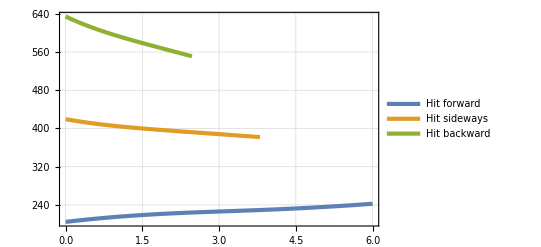

```mathematica
Clear[t]
theme = {"Default","ThickLines","FullAxesGrid"};
r=1000; (*m, radius of cylinder*)
a = 9.81; (*m/s^2, radial acceleration at edge of cylinder*)
ω = Sqrt[a/r]; (*rad/s* angular velocity of cylinder*)
Clear[ω,r]
θ =45 Degree;
speed = 30; (*m/s, ball speed*)

RtoS[t_] := { (*change of basis from Rotating to Fixed (standard) reference frame*)
{-Sin[ω*t],-Cos[ω*t],0,r*Cos[ω*t]},
{Cos[ω*t],-Sin[ω*t],0,r*Sin[ω*t]},
{0,0,1,0},
{0,0,0,1}
};

StoR[t_]:=Simplify[Inverse[RtoS[t]]]; (*change of basis matrix from Fixed to Rotating reference frame*)

posRot = {0,1,0,1}; (*initial position in rotating refernce frame*)
vRot = {0,0,0,0}; (*initial velocity in rotating reference frame*)
Clear[vRot]

vAir[{x_,y_,z_,q_}]:=ω{-y,x,0,0}; (*velocity of air in absolute coordinates*)
Cd = 0.3; (*drag coeficient*)
ρ=1.2; (*kg/m^3, density of air*)
A = 0.004; (*m^2, cross sectional area of ball*)
m = 0.145; (*kg* mass of ball*)
ballAirV[p_,v_] := vAir[p]-v; (*airvelocity of ball as function of position and absolute velocity*)
  
dragForce[p_,v_]:=.5*Cd*A*ρ*Norm[ballAirV[p,v]]^2 *ballAirV[p,v]/Norm[ballAirV[p,v]];(*drag force on ball as function of position and absolute velocity*)
(*dragForce[p_,v_]:={0,0,0,0};*)
Clear[s]

nRadii = 1;
nAngles = 3;
minRad = 500;
maxRad = 500;
minAngle = -90Degree;
maxAngle = 90 Degree;


Zeros[height_,width_]:=Table[0,{i,1,height},{j,1,width}] 
Zeros[size_]:=Zeros[size,size]
locations = Zeros[nRadii,nAngles];
rules = Zeros[nRadii,nAngles];
paths = Zeros[nRadii,nAngles];
velocities = Zeros[nRadii,nAngles];
radii = Array[#&,nRadii,{minRad,maxRad}];
angles = Array[#&,nAngles,{minAngle,maxAngle}];
For[i=1,i≤nRadii,i=i+1,
For[j=1,j≤nAngles,j=j+1,
{
r=radii[[i]],
ϕ=angles[[j]],
ω = Sqrt[a/r],
vRot=speed*{Cos[θ]Sin[ϕ],Sin[θ],Cos[θ]Cos[ϕ],0},
s=NDSolve[
{
m*x''[t]==dragForce[x[t],x'[t]],(*single differential equation*)
x[0]==RtoS[0].posRot,                               (*initial position in fixed frame*)
x'[0]==RtoS'[0].posRot+RtoS[0].vRot,(*initial velocity in fixed frame*)
WhenEvent[Norm[x[t][[{1,2}]]]>=r,{locations[[i,j]]={StoR[t].x[t],t},"StopIntegration"}] (*stop when the ball hits the edge of the cylinder, save the last time and position in end*)
},x,{t,0,1000}
],
rules[[i,j]] = s,
velocities[[i,j]]=Function[t,Evaluate[(x'[t]/.rules[[i,j]])]],
paths[[i,j]]=Function[t,Evaluate[Evaluate[StoR[t]].x[t]/.rules[[i,j]]]]
}
]
]
PlotPath[{s_,end_}]:=ParametricPlot3D[s[t][[1,{1,2,3}]],{t,0,end},PlotStyle->{Thickness[.01],Green}];
eFunc[{s_,end_}]:=Piecewise[{{.5*m*Norm[Evaluate[s[t]][[1,{1,2,3}]]]^2,t≤end}},I];
(*Show[(PlotPath/@(Transpose[{Flatten[paths],Flatten[locations[[All,All,2]]]}]) )~Join~ {ContourPlot3D[(x)^2+(y-500)^2==500^2,{x,-100,100},{y,-10,500},{z,-10,70},Mesh->All,Boxed->False]},PlotRange->All,Boxed->False];*)
withDrag = Plot[
Evaluate[eFunc/@Transpose[{Flatten[velocities],Flatten[locations[[All,All,2]]]}]],
{t,0,6},
Evaluated->True,
PlotLegends->{"Hit forward","Hit sideways","Hit backward"},
PlotTheme->theme
]
```

Part::partw: Part {1,2} of x[t] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part {1,2,3} of InterpolatingFunction[{{0.,7.55432}},«3»,{Automatic}][t] does not exist.

Part::partw: Part {1,2,3} of InterpolatingFunction[{{0.,4.01462}},{5,3,2,{10},{4},{1},0,0,0,Automatic,{},{},False},{{0.,3.97479×10^-6,7.94958×10^-6,«4»,0.914209,1.31169,4.01462}},{{{499.,0.,0.,1.},{-21.2132,69.8956,21.2132,0.},{0.,0.,0.,0.}},{{499.,0.00027782,0.000084318,1.},{-21.2132,69.8956,21.2132,0.},{0.,0.,0.,0.}},{{499.,0.000555641,0.000168636,1.},{-21.2132,69.8956,21.2132,0.},{0.,0.,0.,0.}},«5»,{{471.175,91.6813,27.8251,1.},{-21.2132,69.8956,21.2132,0.},{0.,0.,0.,0.}},{{413.837,280.605,85.163,1.},{-21.2132,69.8956,21.2132,0.},{0.,0.,0.,0.}}},{Automatic}][t] does not exist.

Part::partw: Part {1,2,3} of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

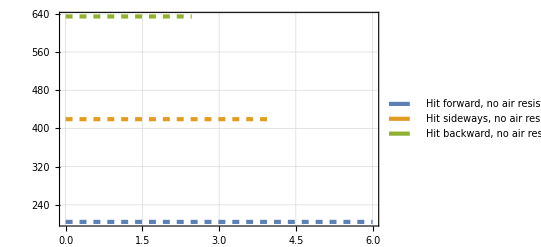

```mathematica
dragForce[p_,v_]:={0,0,0,0};
For[i=1,i≤nRadii,i=i+1,
For[j=1,j≤nAngles,j=j+1,
{
r=radii[[i]],
ϕ=angles[[j]],
ω = Sqrt[a/r],
vRot=speed*{Cos[θ]Sin[ϕ],Sin[θ],Cos[θ]Cos[ϕ],0},
s=NDSolve[
{
m*x''[t]==dragForce[x[t],x'[t]],(*single differential equation*)
x[0]==RtoS[0].posRot,                               (*initial position in fixed frame*)
x'[0]==RtoS'[0].posRot+RtoS[0].vRot,(*initial velocity in fixed frame*)
WhenEvent[Norm[x[t][[{1,2}]]]>=r,{locations[[i,j]]={StoR[t].x[t],t},"StopIntegration"}] (*stop when the ball hits the edge of the cylinder, save the last time and position in end*)
},x,{t,0,1000}
],
rules[[i,j]] = s,
velocities[[i,j]]=Function[t,Evaluate[(x'[t]/.rules[[i,j]])]],
paths[[i,j]]=Function[t,Evaluate[Evaluate[StoR[t]].x[t]/.rules[[i,j]]]]
}
]
]
PlotPath[{s_,end_}]:=ParametricPlot3D[s[t][[1,{1,2,3}]],{t,0,end},PlotStyle->{Thickness[.01],Green}];
eFunc[{s_,end_}]:=Piecewise[{{.5*m*Norm[Evaluate[s[t]][[1,{1,2,3}]]]^2,t≤end}},I];
(*Show[(PlotPath/@(Transpose[{Flatten[paths],Flatten[locations[[All,All,2]]]}]) )~Join~ {ContourPlot3D[(x)^2+(y-500)^2==500^2,{x,-100,100},{y,-10,500},{z,-10,70},Mesh->All,Boxed->False]},PlotRange->All,Boxed->False];*)
withoutDrag = Plot[
Evaluate[eFunc/@Transpose[{Flatten[velocities],Flatten[locations[[All,All,2]]]}]],
{t,0,6},
PlotTheme->theme,
PlotStyle->Dashed,
PlotLegends->{"Hit forward, no air resistance","Hit sideways, no air resistance","Hit backward, no air resistance"}
]
```

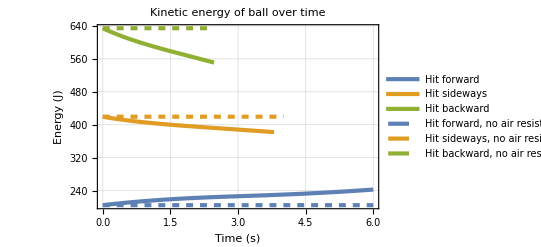

```mathematica
Show[withDrag,withoutDrag,AxesOrigin->{0,0},PlotRange->{{0,All},{0,All}},LabelStyle->Directive[Black,Bold,Larger],
PlotLabel->"Kinetic energy of ball over time",
FrameLabel->{"Time (s)","Energy (J)"}
]
```